## generate archetypes

```mathematica
sevenSegmentDefs={{1,2,4,5,6,7},{2,5},{6,5,3,4,1},{6,5,3,2,1},{7,3,5,2},{6,7,3,2,1},{6,7,3,4,2,1},{6,5,2},{1,2,3,4,5,6,7},{1,2,3,5,6,7}};
```

```mathematica
sevenSegmentImages=Table[
Graphics[{
Black,
White,Rectangle[{0,0},{5,9}],
(*Table[Line[{{0,h},{5,h}}],{h,0,9}],
Table[Line[{{v,0},{v,9}}],{v,0,5}],*)
Black,
{
(*1*){Triangle[{{0.5,0.5},{1,0},{1,1}}],Rectangle[{1,0},{4,1}],Triangle[{{4,0},{4,1},{4.5,0.5}}]},
(*2*){Triangle[{{4,4},{4.5,4.5},{5,4}}],Rectangle[{4,1},{5,4}],Triangle[{{4.5,0.5},{5,1},{4,1}}]},
(*3*){Triangle[{{0.5,4.5},{1,4},{1,5}}],Rectangle[{1,4},{4,5}],Triangle[{{4,4},{4,5},{4.5,4.5}}]},
(*4*){Triangle[{{0,4},{0.5,4.5},{1,4}}],Rectangle[{0,1},{1,4}],Triangle[{{0.5,0.5},{1,1},{0,1}}]},
(*5*){Triangle[{{4,8},{4.5,8.5},{5,8}}],Rectangle[{4,5},{5,8}],Triangle[{{4.5,4.5},{5,5},{4,5}}]},
(*6*){Triangle[{{0.5,8.5},{1,8},{1,9}}],Rectangle[{1,8},{4,9}],Triangle[{{4,8},{4,9},{4.5,8.5}}]},
(*7*){Triangle[{{0,8},{0.5,8.5},{1,8}}],Rectangle[{0,5},{1,8}],Triangle[{{0.5,4.5},{1,5},{0,5}}]}
}[[number]]
}],{number,sevenSegmentDefs}];
```

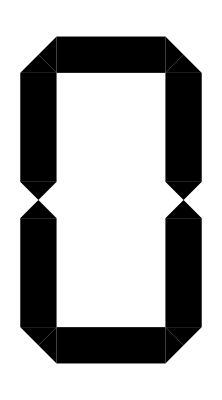
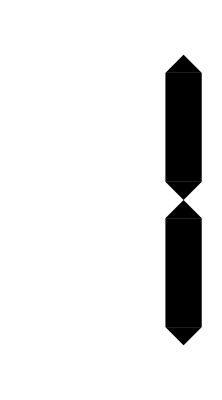
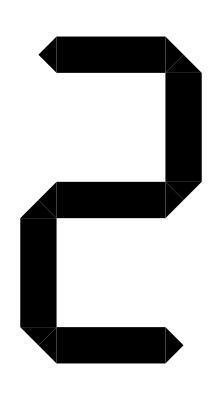
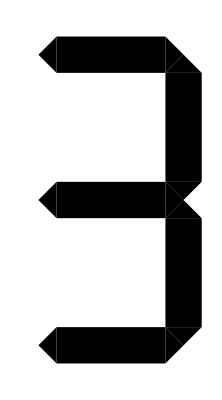
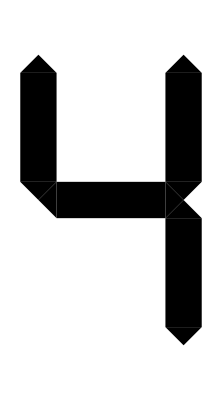
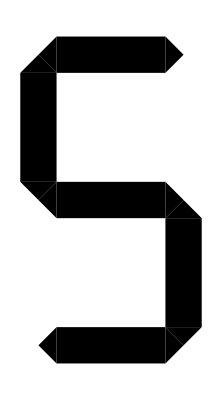
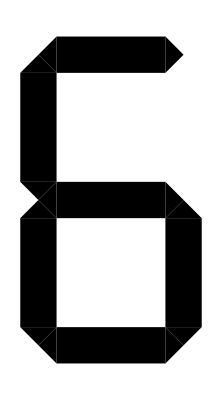
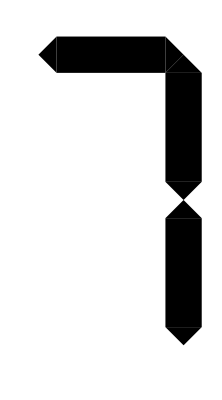

```mathematica
Row[sevenSegmentImages]
```

```mathematica
Table[Export[NotebookDirectory[]<>"\\archetype_"<>ToString[n]<>".png",sevenSegmentImages[[n+1]]],{n,0,9}]
```

{C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\heatmeter_images\ocr_attempt\\archetype_0.png,C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\heatmeter_images\ocr_attempt\\archetype_1.png,C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\heatmeter_images\ocr_attempt\\archetype_2.png,C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\heatmeter_images\ocr_attempt\\archetype_3.png,C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\heatmeter_images\ocr_attempt\\archetype_4.png,C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\heatmeter_images\ocr_attempt\\archetype_5.png,C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\heatmeter_images\ocr_attempt\\archetype_6.png,C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\heatmeter_images\ocr_attempt\\archetype_7.png,C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\heatmeter_images\ocr_attempt\\archetype_8.png,C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\heatmeter_images\ocr_attempt\\archetype_9.png}

## preprocess

```mathematica
img=ColorConvert[Import["C:\\Users\\Beno\\Documents\\SZAKI\\kazankontroll-dashboard\\heatmeter_images\\ocr_attempt\\image.jpg"],"Grayscale"];
```

```mathematica
ImageResize[Image[Round[ImageData[ImageGrayscaleShifter[ImageRotate[img,Pi/2]]]]],Round[ImageDimensions[img][[{2,1}]]/2]]
```

-Graphics-

```mathematica
EdgeDetectorFromScratch[ImageGrayscaleShifter[Image[1-ImageData[ImageResize[Image[Round[ImageData[ImageGrayscaleShifter[ImageRotate[img,Pi/2]]]]],Round[ImageDimensions[img][[{2,1}]]/2]]]]]
]
```

-Graphics-

```mathematica
EdgeDetect[image]
```

```mathematica
EdgeDetectorFromScratch[image_Image]:=Module[{gray,gx,gy,gradientMagnitude},(*Convert to grayscale*)gray=ColorConvert[image,"Grayscale"];
(*Sobel kernels for x and y directions*)gx={{-1,0,1},{-2,0,2},{-1,0,1}};
gy={{-1,-2,-1},{0,0,0},{1,2,1}};
(*Apply convolution to find gradients*)gradientX=ImageConvolve[gray,gx];
gradientY=ImageConvolve[gray,gy];
(*Combine gradients to find edge magnitude*)gradientMagnitude=Sqrt[ImageData[gradientX]^2+ImageData[gradientY]^2];
(*Convert back to image*)Image[gradientMagnitude]]
```

```mathematica
EdgeDetectorFromScratch[img]
```

-Graphics-

## recognizer

```mathematica
Manipulate[
Row[{
img,
ListPlot[
Table[
{factor,Total[MapToZeroAndOne[Clip[Flatten[ImageData[img]]+factor Mean[Flatten[ImageData[img]]],{0,1}]]]}
,{factor,-1,1,0.1}],Epilog->{
Thick,Red,Line[{{factor,-100},{factor,500}}],
Thick,Green,Line[{{
Table[
{factor,Total[MapToZeroAndOne[Clip[Flatten[ImageData[img]]+(factor+0.05) Mean[Flatten[ImageData[img]]],{0,1}]]]-Total[MapToZeroAndOne[Clip[Flatten[ImageData[img]]+factor Mean[Flatten[ImageData[img]]],{0,1}]]]}
,{factor,-1,1,0.05}]//#[[MinPosition[Transpose[#][[2]]]]][[1]]&,
-100
},{
Table[
{factor,Total[MapToZeroAndOne[Clip[Flatten[ImageData[img]]+(factor+0.05) Mean[Flatten[ImageData[img]]],{0,1}]]]-Total[MapToZeroAndOne[Clip[Flatten[ImageData[img]]+factor Mean[Flatten[ImageData[img]]],{0,1}]]]}
,{factor,-1,1,0.05}]//#[[MinPosition[Transpose[#][[2]]]]][[1]]&,
500
}}]
},Joined->True,Filling->Axis,FillingStyle->Black,PlotStyle->Black
],
Image[ArrayReshape[MapToZeroAndOne[Clip[Flatten[ImageData[img]]+factor Mean[Flatten[ImageData[img]]],{0,1}]],ImageDimensions[img][[{2,1}]]]],
ListPlot[
Table[
{factor,Total[MapToZeroAndOne[Clip[Flatten[ImageData[img]]+(factor+0.05) Mean[Flatten[ImageData[img]]],{0,1}]]]-Total[MapToZeroAndOne[Clip[Flatten[ImageData[img]]+factor Mean[Flatten[ImageData[img]]],{0,1}]]]}
,{factor,-1,1,0.1}],Epilog->{
Thick,Red,Line[{{factor,-100},{factor,500}}],
Thick,Green,Line[{{
Table[
{factor,Total[MapToZeroAndOne[Clip[Flatten[ImageData[img]]+(factor+0.05) Mean[Flatten[ImageData[img]]],{0,1}]]]-Total[MapToZeroAndOne[Clip[Flatten[ImageData[img]]+factor Mean[Flatten[ImageData[img]]],{0,1}]]]}
,{factor,-1,1,0.05}]//#[[MinPosition[Transpose[#][[2]]]]][[1]]&,
-100
},{
Table[
{factor,Total[MapToZeroAndOne[Clip[Flatten[ImageData[img]]+(factor+0.05) Mean[Flatten[ImageData[img]]],{0,1}]]]-Total[MapToZeroAndOne[Clip[Flatten[ImageData[img]]+factor Mean[Flatten[ImageData[img]]],{0,1}]]]}
,{factor,-1,1,0.05}]//#[[MinPosition[Transpose[#][[2]]]]][[1]]&,
500
}}]
},Joined->True,FillingStyle->Black,PlotStyle->Black
],
Image[ArrayReshape[Round[Flatten[ImageData[img]]+factor Mean[Flatten[ImageData[img]]]],ImageDimensions[img][[{2,1}]]]],
ListPlot[
Table[
{factor,Total[Round[Flatten[ImageData[img]]+(factor+0.05) Mean[Flatten[ImageData[img]]]]]-Total[Round[Flatten[ImageData[img]]+factor Mean[Flatten[ImageData[img]]]]]}
,{factor,-1,1,0.1}],Epilog->{
Thick,Red,Line[{{factor,-100},{factor,500}}],
Thick,Green,Line[{{
Table[
{factor,Total[Round[Flatten[ImageData[img]]+(factor+0.05) Mean[Flatten[ImageData[img]]]]]-Total[Round[Flatten[ImageData[img]]+factor Mean[Flatten[ImageData[img]]]]]}
,{factor,-1,1,0.1}]//#[[MinPosition[Transpose[#][[2]]]]][[1]]&,
-100
},{
Table[
{factor,Total[Round[Flatten[ImageData[img]]+(factor+0.05) Mean[Flatten[ImageData[img]]]]]-Total[Round[Flatten[ImageData[img]]+factor Mean[Flatten[ImageData[img]]]]]}
,{factor,-1,1,0.1}]//#[[MinPosition[Transpose[#][[2]]]]][[1]]&,
500
}}]
},Joined->True,FillingStyle->Black,PlotStyle->Black
]
}],
{img,trials},
{{factor,0},-1,1,0.01}
]
```

```mathematica
MaxPosition[list_]:=Position[list,Max[list]][[1]][[1]]
```

```mathematica
MinPosition[list_]:=Position[list,Min[list]][[1]][[1]]
```

```mathematica
ImageGrayscaleShifter[img_]:=Module[
{imgVector,meanFactor},
imgVector=Flatten[ImageData[img]];
meanFactor=Max[
{Table[
{factor,Total[MapToZeroAndOne[Clip[imgVector+(factor+0.05) 0.5,{0,1}]]]-Total[MapToZeroAndOne[Clip[imgVector+factor 0.5,{0,1}]]]}
,{factor,-1,1,0.05}]//#[[MinPosition[Transpose[#][[2]]]]][[1]]&,
Table[
{factor,Total[Round[imgVector+(factor+0.05) 0.5]]-Total[Round[imgVector+factor 0.5]]}
,{factor,-1,1,0.05}]//#[[MinPosition[Transpose[#][[2]]]]][[1]]&
}
];
Image[ArrayReshape[MapToZeroAndOne[Clip[imgVector+meanFactor 0.5,{0,1}]],ImageDimensions[img][[{2,1}]]]]
]
```

```mathematica
unknown=Import[NotebookDirectory[]<>"trial.jpg"]
```

-Graphics-

```mathematica
pixelNum=ImageDimensions[unknown]//#[[1]]#[[2]]&
```

300

```mathematica
archetypes=Table[ColorConvert[Import[NotebookDirectory[]<>"archetypes\\archetype_"<>ToString[n]<>".png"],"Grayscale"],{n,0,9}];
```

```mathematica
archetypeDimensions=ImageDimensions[archetypes[[1]]];
```

```mathematica
tests=Table[ColorConvert[ImageResize[Import[NotebookDirectory[]<>"archetype_"<>ToString[n]<>".png"],{12,25}],"Grayscale"],{n,0,9}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
truth=Range[0,9]
```

{0,1,2,3,4,5,6,7,8,9}

```mathematica
testRes=Table[
processedUnknown=Image[ImageData[unknown]//ArrayReshape[Flatten[#]+Mean[Flatten[#]],Dimensions[#]]&//ArrayReshape[Round[Flatten[#]/Max[#]],Dimensions[#]]&];
unknownVector=1-Flatten[ImageData[processedUnknown],1];
pixelNum=ImageDimensions[processedUnknown]//#[[1]]#[[2]]&;
Table[
Table[
Table[
Table[
Module[
{paddedArchetype,paddedHShiftedArchetype,paddedVHShiftedArchetype,archetypeVector},
paddedArchetype=ImageData[ImageResize[Image[ArrayPad[ImageData[archetypes[[num+1]]],Round[archetypeDimensions padding],1]],ImageDimensions[unknown]]];
paddedHShiftedArchetype=Map[
If[
horizontalShift<0,
Drop[Join[#,ConstantArray[1,Round[Length[#]Abs[horizontalShift]]]],Round[Length[#]Abs[horizontalShift]]],
Drop[Join[ConstantArray[1,Round[Length[#]horizontalShift]],#],-Round[Length[#]horizontalShift]],
#
]&,
paddedArchetype
];
paddedVHShiftedArchetype=Transpose[Map[
If[
verticalShift<0,
Drop[Join[#,ConstantArray[1,Round[Length[#]Abs[verticalShift]]]],Round[Length[#]Abs[verticalShift]]],
Drop[Join[ConstantArray[1,Round[Length[#]verticalShift]],#],-Round[Length[#]verticalShift]],
#
]&,
Transpose[paddedHShiftedArchetype]
]];
archetypeVector=1-Round[Flatten[paddedVHShiftedArchetype]];
{
unknown,
processedUnknown,
paddedShiftedArchetype,
N[(unknownVector.archetypeVector)/Mean[{Total[unknownVector],Total[archetypeVector]}]]
}
]
,{num,0,9}]
,{verticalShift,-0.1,0.1,0.05}]
,{horizontalShift,-0.1,0.1,0.05}]
,{padding,0.05,0.2,0.05}]
,{unknown,tests}];
```

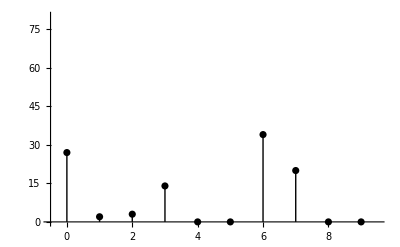
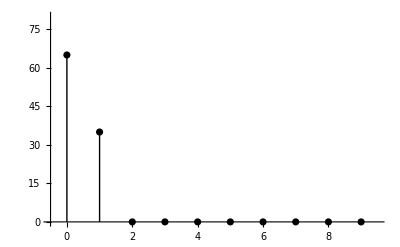
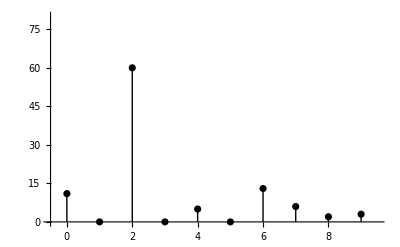
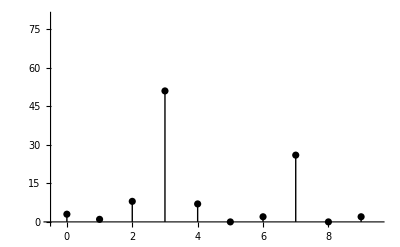
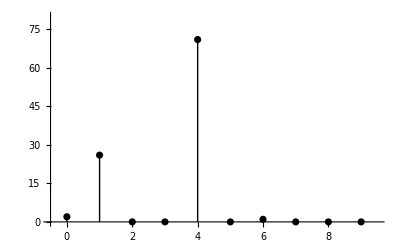
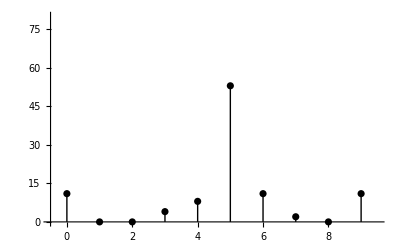
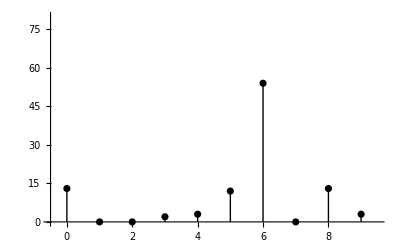
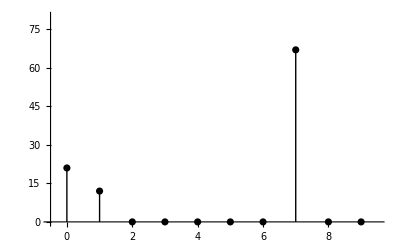
-Graphics- | 0 | -Graphics-
-Graphics- | 0 | -Graphics-
-Graphics- | 2 | -Graphics-
-Graphics- | 2 | -Graphics-
-Graphics- | 5 | -Graphics-
-Graphics- | 3 | -Graphics-
-Graphics- | 3 | -Graphics-
-Graphics- | 2 | -Graphics-
-Graphics- | 1 | -Graphics-
-Graphics- | 3 | -Graphics-

```mathematica
Table[
{
tests[[trial]],
truth[[trial]],
ListPlot[
Map[
{#,
Length[Flatten[Position[
Map[
Range[0,9][[MaxPosition[Transpose[#][[4]]]]]&,
Flatten[testRes[[trial]],2]],
#
]]]
}&
,Range[0,9]],PlotStyle->Black,AxesOrigin->{-0.5,0},
PlotRange->{{-0.5,9.5},{0,80}},Ticks->{Range[0,9],Automatic},
Filling->Axis,FillingStyle->{Thick,Black}
]
}
,{trial,1,Length[tests]}]//Grid
```

```mathematica
testRes//Dimensions
```

{10,4,5,5,10,4}

```mathematica
trials=Map[ImageGrayscaleShifter[Import[#]]&,Flatten[Table[Table[Table[NotebookDirectory[]<>"\\testchars\\mod_image_"<>ToString[image]<>"_"<>ToString[cycle]<>"_slice_"<>ToString[char]<>".jpg",{char,1,4}],{cycle,1,4}],{image,1,3}]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
truth={5,3,3,2,1,3,0,6,0,1,4,3,0,0,3,2,3,4,5,4,3,0,4,0,-1,0,-1,-1,1,0,3,9,5,3,3,2,8,0,4,0,6,6,7,7,1,0,7,9};
```

```mathematica
Grid[{truth,trials}]
```

5 | 3 | 3 | 2 | 1 | 3 | 0 | 6 | 0 | 1 | 4 | 3 | 0 | 0 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 0 | 4 | 0 | -1 | 0 | -1 | -1 | 1 | 0 | 3 | 9 | 5 | 3 | 3 | 2 | 8 | 0 | 4 | 0 | 6 | 6 | 7 | 7 | 1 | 0 | 7 | 9
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
trials=Map[ColorConvert[Import[#],"Grayscale"]&,Flatten[Table[Table[NotebookDirectory[]<>"\\testchars\\best_case\\"<>ToString[cycle]<>"_"<>ToString[char]<>".jpg",{char,1,4}],{cycle,1,4}]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
truth={0,0,2,2,5,3,3,2,1,3,0,6,0,1,4,3};
```

```mathematica
Grid[{truth,trials}]
```

0 | 0 | 2 | 2 | 5 | 3 | 3 | 2 | 1 | 3 | 0 | 6 | 0 | 1 | 4 | 3
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
archetypes=Table[ColorConvert[Import[NotebookDirectory[]<>"archetypes\\archetype_"<>ToString[n]<>".png"],"Grayscale"],{n,0,9}];
```

```mathematica
archetypeDimensions=ImageDimensions[archetypes[[1]]];
```

```mathematica
trials=Map[ColorConvert[Import[#],"Grayscale"]&,RandomSample[Drop[FileNames[All,NotebookDirectory[]<>"\\testchars\\"],-1],30]]
```

```mathematica
trials={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
truth={2,0,6,9,7,3,4,6,3,0,1,3,3,1,0,7,-1,1,4,0,5,0,0,3,3,2,-1,0,1,4};
```

```mathematica
Grid[{truth,trials}]
```

2 | 0 | 6 | 9 | 7 | 3 | 4 | 6 | 3 | 0 | 1 | 3 | 3 | 1 | 0 | 7 | -1 | 1 | 4 | 0 | 5 | 0 | 0 | 3 | 3 | 2 | -1 | 0 | 1 | 4
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
trialRes=ParallelTable[
unknownVector=1-Flatten[ImageData[unknown],1];
pixelNum=ImageDimensions[unknown]//#[[1]]#[[2]]&;
Table[
Table[
Table[
Module[
{padded8,paddedHShifted8,paddedVHShifted8,vector8,sevenSegmentPixels},
padded8=ImageData[ImageResize[Image[ArrayPad[ImageData[archetypes[[8+1]]],Round[archetypeDimensions padding],1]],ImageDimensions[unknown]]];
paddedHShifted8=Map[
If[
horizontalShift<0,
Drop[Join[#,ConstantArray[1,Round[Length[#]Abs[horizontalShift]]]],Round[Length[#]Abs[horizontalShift]]],
Drop[Join[ConstantArray[1,Round[Length[#]horizontalShift]],#],-Round[Length[#]horizontalShift]],
#
]&,
padded8
];
paddedVHShifted8=Transpose[Map[
If[
verticalShift<0,
Drop[Join[#,ConstantArray[1,Round[Length[#]Abs[verticalShift]]]],Round[Length[#]Abs[verticalShift]]],
Drop[Join[ConstantArray[1,Round[Length[#]verticalShift]],#],-Round[Length[#]verticalShift]],
#
]&,
Transpose[paddedHShifted8]
]];
sevenSegmentPixels=Flatten[Position[Round[Flatten[paddedVHShifted8]],0]];
Table[
Module[
{paddedArchetype,paddedHShiftedArchetype,paddedVHShiftedArchetype,archetypeVector},
paddedArchetype=ImageData[ImageResize[Image[ArrayPad[ImageData[archetypes[[num+1]]],Round[archetypeDimensions padding],1]],ImageDimensions[unknown]]];
paddedHShiftedArchetype=Map[
If[
horizontalShift<0,
Drop[Join[#,ConstantArray[1,Round[Length[#]Abs[horizontalShift]]]],Round[Length[#]Abs[horizontalShift]]],
Drop[Join[ConstantArray[1,Round[Length[#]horizontalShift]],#],-Round[Length[#]horizontalShift]],
#
]&,
paddedArchetype
];
paddedVHShiftedArchetype=Transpose[Map[
If[
verticalShift<0,
Drop[Join[#,ConstantArray[1,Round[Length[#]Abs[verticalShift]]]],Round[Length[#]Abs[verticalShift]]],
Drop[Join[ConstantArray[1,Round[Length[#]verticalShift]],#],-Round[Length[#]verticalShift]],
#
]&,
Transpose[paddedHShiftedArchetype]
]];
archetypeVector=1-Round[Flatten[paddedVHShiftedArchetype]];
{
unknown,
paddedVHShiftedArchetype,
(*N[(unknownVector.archetypeVector)/Mean[{Total[unknownVector],Total[archetypeVector]}]],*)
Count[MapThread[Equal,{Round[unknownVector[[sevenSegmentPixels]]],Round[archetypeVector[[sevenSegmentPixels]]]}],True]/Length[sevenSegmentPixels],
padding,
horizontalShift,
verticalShift
}
]
,{num,0,9}]]
,{verticalShift,-0.1,0.1+0.05,0.05}]
,{horizontalShift,0,0.25+0.05,0.05}]
,{padding,0.05,0.25+0.05,0.05}]
,{unknown,trials[[{1,2,3}]]}];
```

```mathematica
Transpose[Flatten[trialRes[[1]],2][[1]]][[3]]//N
```

{0.395884,0.727603,0.447942,0.455206,0.408596,0.281477,0.215496,0.705811,0.232446,0.298426}

```mathematica
paddingList=Table[padding,{padding,0.05,0.25+0.05,0.05}];
horizontalShiftList=Table[horizontalShift,{horizontalShift,0,0.25+0.05,0.05}];
verticalShiftList=Table[verticalShift,{verticalShift,-0.1,0.1+0.05,0.05}];
```

```mathematica
Table[
{
trials[[trial]],
truth[[trial]],
ListPlot[
Map[
{#,
Length[Flatten[Position[
Map[
Range[0,9][[MaxPosition[Transpose[#][[3]]]]]&,
Flatten[trialRes[[trial]],2]],
#
]]]
}&
,Range[0,9]],PlotStyle->Black,AxesOrigin->{-0.5,0},
PlotRange->{{-0.5,9.5},All},Ticks->{Range[0,9],Automatic},
Filling->Axis,FillingStyle->{Thick,Black}
]
}
,{trial,1,Length[trials]}]//Grid
```

Part::partw: Part 4 of {<<929089192 bytes>>} does not exist.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of Transpose[4] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1⟧ cannot be used as a part specification.

Part::pkspec1: The expression {0,1,2,3,4,5,6,7,8,9}⟦{}⟦1⟧⟧ cannot be used as a part specification.

Part::pkspec1: The expression {}⟦1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

$Aborted

```mathematica
trialResEvaluation=Flatten[Table[Table[Table[Table[{
paddingList[[padLevel]],
horizontalShiftList[[hLevel]],
verticalShiftList[[vLevel]],
truth[[trial]],
Reverse[SortBy[Transpose [{
Range[0,9],
Map[
#[[3]]&,trialRes[[trial]][[padLevel]][[hLevel]][[vLevel]]
]}],#[[2]]&]][[1]][[1]],
Total[Abs[Differences[Sort[Map[
#[[3]]&,trialRes[[trial]][[padLevel]][[hLevel]][[vLevel]]
]]]]],
Differences[Transpose[Reverse[SortBy[Transpose [{
Range[0,9],
Map[
#[[3]]&,trialRes[[trial]][[padLevel]][[hLevel]][[vLevel]]
]}],#[[2]]&]]][[2]]][[1]]
},{vLevel,1,Length[verticalShiftList]}],{hLevel,1,Length[horizontalShiftList]}],{padLevel,1,Length[paddingList]}],{trial,1,Length[trials]}],3];
```

```mathematica
mLabels={"pad","h shift","v shift","pred","truth","total gradient","first gradient"};
```

```mathematica
hits=Select[trialResEvaluation,#[[4]]==#[[5]]&];
misses=Select[trialResEvaluation,#[[4]]!=#[[5]]&];
```

```mathematica
100Length[hits]/Length[trialResEvaluation]//N
100Length[misses]/Length[trialResEvaluation]//N
```

32.1164

67.8836

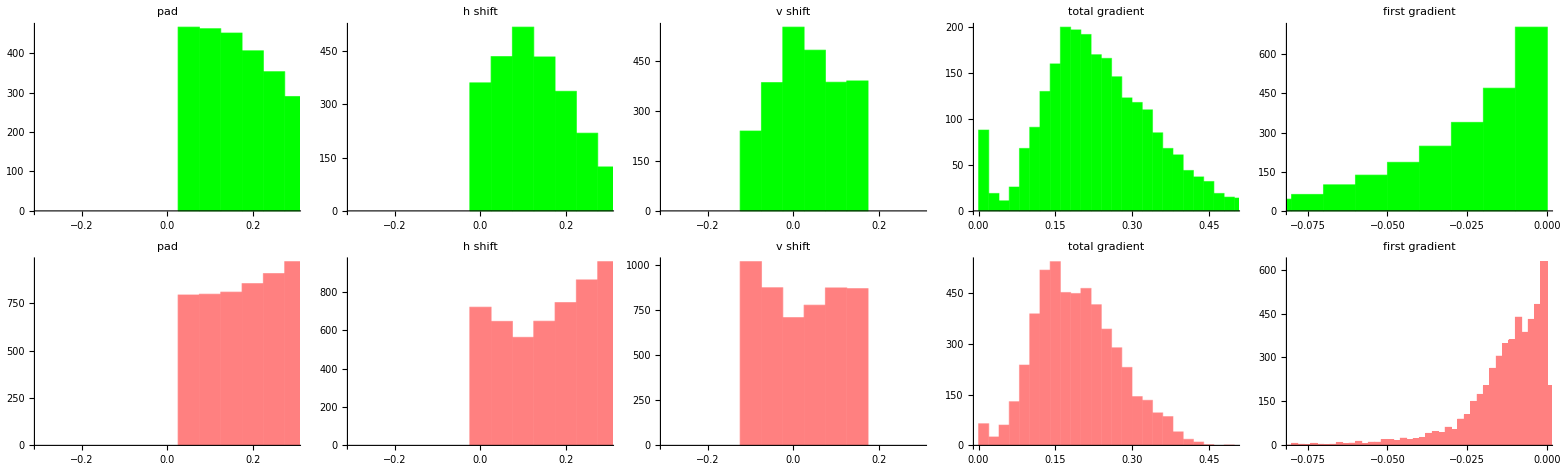

```mathematica
Table[Table[
Histogram[
Transpose[{hits,misses}[[hitOrMiss]]][[m]],
ChartStyle->{Green,Pink}[[hitOrMiss]],PlotLabel->mLabels[[m]],ImageSize->200,
PlotRange->{{{-0.3,0.3},{-0.3,0.3},{-0.3,0.3},Automatic,Automatic,{0,0.5},{-0.08,0}}[[m]],All}
]
,{m,{1,2,3,6,7}}],{hitOrMiss,1,2}]//Grid
```

```mathematica
selectionCriteria={{0.05,0.25},{0,0.25},{-0.1,0.1},{0,9},{0,9},{0.6,10},{-1,-0.015}};
```

```mathematica
trialResEvaluation[[1]]
```

{0.05,0.,-0.1,2,0,0.335117,-0.0179833}

```mathematica
selectedTrialResEvaluation=Select[
trialResEvaluation,
1==Mean[Boole[Table[
Between[#[[m]],selectionCriteria[[m]]]
,{m,1,7}]]]&
];
```

```mathematica
hits=Select[selectedTrialResEvaluation,#[[4]]==#[[5]]&];
misses=Select[selectedTrialResEvaluation,#[[4]]!=#[[5]]&];
```

```mathematica
100Length[hits]/Length[trialResEvaluation]//N
100Length[misses]/Length[trialResEvaluation]//N
```

12.1561

7.94974

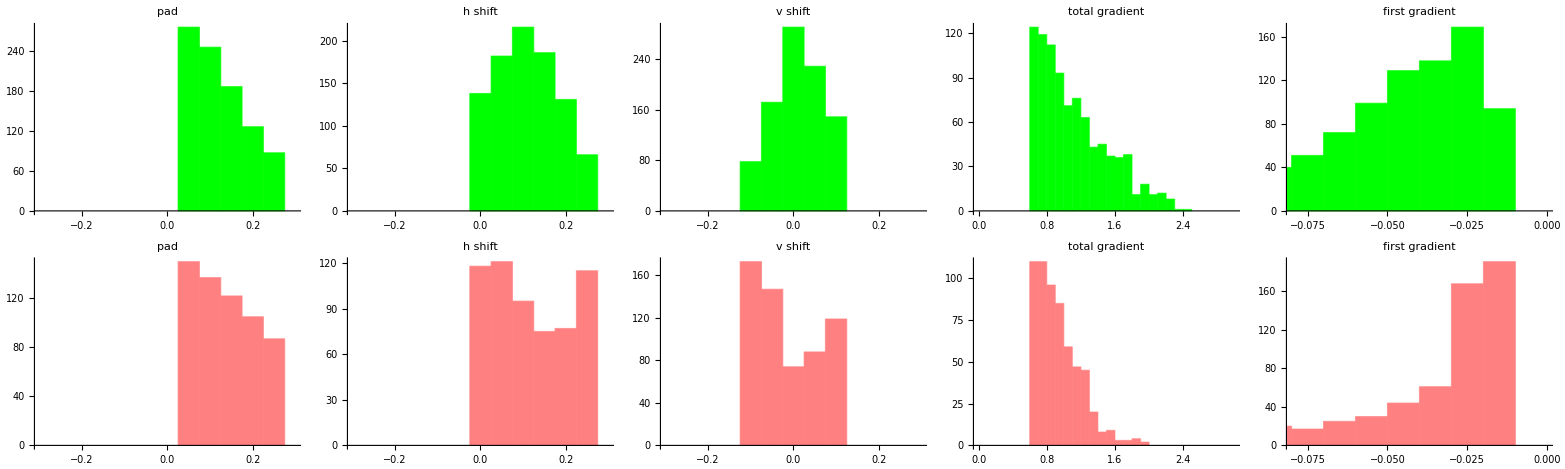

```mathematica
Table[Table[
Histogram[
Transpose[{hits,misses}[[hitOrMiss]]][[m]],
ChartStyle->{Green,Pink}[[hitOrMiss]],PlotLabel->mLabels[[m]],ImageSize->200,
PlotRange->{{{-0.3,0.3},{-0.3,0.3},{-0.3,0.3},Automatic,Automatic,{0,3},{-0.08,0}}[[m]],All}
]
,{m,{1,2,3,6,7}}],{hitOrMiss,1,2}]//Grid
```

```mathematica
trialResFlat=Map[Flatten[#,2]&,trialRes];
```

```mathematica
Total[Abs[Differences[Reverse[Sort[Transpose[trialResFlat[[trial]][[1]]][[3]]]]]]]
```

0.149893

```mathematica
activation = Transpose[trialResFlat[[trial]][[1]]][[3]]
```

{0.290245,0.250339,0.252213,0.257383,0.194587,0.140353,0.183178,0.272262,0.263868,0.233035}

```mathematica
activation={0.33124371647222606,0.17396046203860324,0.2283684735246958,0.2365337213555333,0.29949976160054936,0.28604721942538774,0.32628574163896035,0.197249917789996,0.3465009447572945,0.3110780362382277};
```

```mathematica
gradient = Differences[Sort[activation]]
```

{0.0232895,0.0311186,0.00816525,0.0495135,0.0134525,0.0115783,0.0152077,0.00495797,0.0152572}

```mathematica
Total[gradient]
```

0.17254

```mathematica
gradient[[-1]]
```

0.0152572

```mathematica
passed=Table[
Select[
trialResFlat[[trial]],
0.18<Total[Abs[Differences[Reverse[Sort[Transpose[#][[3]]]]]]]&&
Differences[Reverse[Sort[Transpose[#][[3]]]]][[1]]<-0.03
&]
,{trial,1,Length[trials]}];
Map[Length,passed]
Table[
{truth[[trial]],Commonest[Map[
Reverse[SortBy[Transpose[{Range[0,9],Transpose[#][[3]]}],#[[2]]&]][[1]][[1]]
&,passed[[trial]]],1][[1]]}
,{trial,1,Length[trials]}]
Mean[Table[
Boole[{truth[[trial]]==Commonest[Map[
Reverse[SortBy[Transpose[{Range[0,9],Transpose[#][[3]]}],#[[2]]&]][[1]][[1]]
&,passed[[trial]]],1][[1]]}]
,{trial,1,Length[trials]}]][[1]]//N
```

{49,21,15,7,33,37,30,22,25,15,105,18,31,123,32,73,22,137,88,16,18,17,11,10,32,78,5,4,27,104}

{{2,2},{0,0},{6,6},{9,9},{7,7},{3,3},{4,4},{6,6},{3,3},{0,0},{1,1},{3,7},{3,3},{1,1},{0,0},{7,7},{-1,0},{1,1},{4,4},{0,0},{5,5},{0,0},{0,0},{3,3},{3,7},{2,7},{-1,0},{0,0},{1,7},{4,4}}

0.8

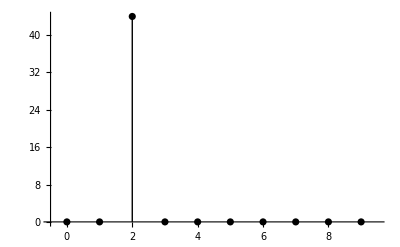
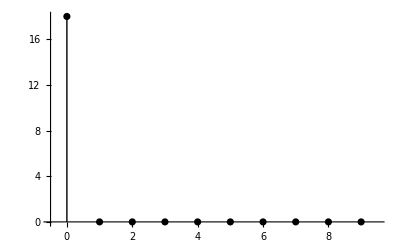
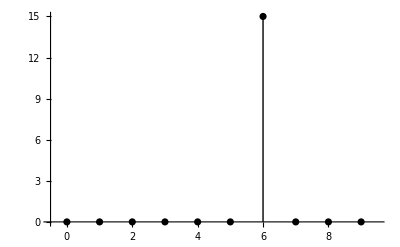
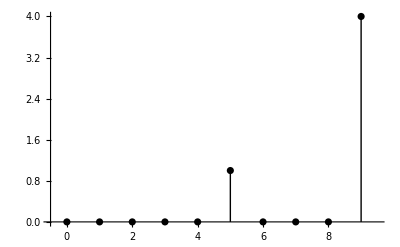
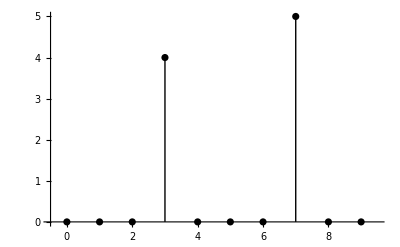
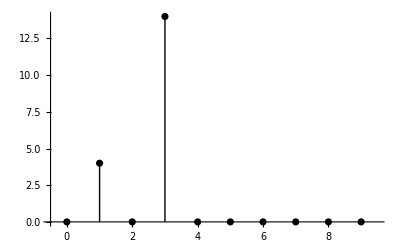
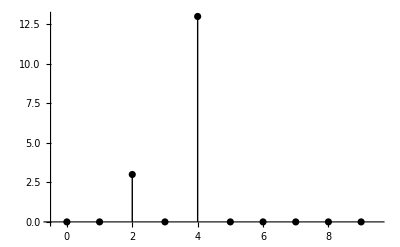
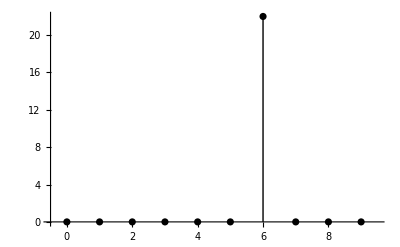
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Table[
{trials[[trial]],
ListPlot[Table[
{n,
Length[Position[
Map[
Reverse[SortBy[Transpose[{Range[0,9],Transpose[#][[3]]}],#[[2]]&]][[1]][[1]]
&,passed[[trial]]],
n]]
}
,{n,0,9}],PlotStyle->Black,AxesOrigin->{-0.5,0},
PlotRange->{{-0.5,9.5},All},Ticks->{Range[0,9],Automatic},
Filling->Axis,FillingStyle->{Thick,Black}
]
}
,{trial,1,Length[trials]}]//Grid
```

## to Python

```mathematica
unknown=ColorConvert[Import[NotebookDirectory[]<>"batch\\chars\\20231118-113016374_2_2.jpg"],"Grayscale"]
```

-Graphics-

```mathematica
unknownVector=1-Flatten[ImageData[unknown],1];
pixelNum=ImageDimensions[unknown]//#[[1]]#[[2]]&;
activations=Flatten[ParallelTable[
Table[
Table[
Table[
Module[
{paddedArchetype,paddedHShiftedArchetype,paddedVHShiftedArchetype,archetypeVector},
paddedArchetype=ImageData[ImageResize[Image[ArrayPad[ImageData[archetypes[[num+1]]],Round[archetypeDimensions padding],1]],ImageDimensions[unknown]]];
paddedHShiftedArchetype=Map[
If[
horizontalShift<0,
Drop[Join[#,ConstantArray[1,Round[Length[#]Abs[horizontalShift]]]],Round[Length[#]Abs[horizontalShift]]],
Drop[Join[ConstantArray[1,Round[Length[#]horizontalShift]],#],-Round[Length[#]horizontalShift]],
#
]&,
paddedArchetype
];
paddedVHShiftedArchetype=Transpose[Map[
If[
verticalShift<0,
Drop[Join[#,ConstantArray[1,Round[Length[#]Abs[verticalShift]]]],Round[Length[#]Abs[verticalShift]]],
Drop[Join[ConstantArray[1,Round[Length[#]verticalShift]],#],-Round[Length[#]verticalShift]],
#
]&,
Transpose[paddedHShiftedArchetype]
]];
archetypeVector=1-Round[Flatten[paddedVHShiftedArchetype]];
{
num,
N[(unknownVector.archetypeVector)/Mean[{Total[unknownVector],Total[archetypeVector]}]]
}
]
,{num,0,9}]
,{verticalShift,-0.1,0.1,0.05}]
,{horizontalShift,0,0.25,0.05}]
,{padding,0.05,0.25,0.05}],2];
```

```mathematica
activations//Dimensions
```

{150,10,2}

```mathematica
activations[[1]]
```

{{0,0.436489},{1,0.230269},{2,0.35439},{3,0.351566},{4,0.370823},{5,0.357402},{6,0.397256},{7,0.291418},{8,0.45819},{9,0.426562}}

```mathematica
Commonest[Map[
SortBy[#,Last][[-1]][[1]]&,
Select[
activations,
0.15<Total[Differences[Sort[Transpose[#][[2]]]]]&&
0.02<Differences[Sort[Transpose[#][[2]]]][[-1]]
&]
]][[1]]
```

3